# MAT: 150 -- Lab 6

## Solution

Consider the matrix A = {{1,2,3},{1,-2,1}} and vector b = {1,1}. Note that the rows of A are orthogonal and the system Ax=b is consistent. Write the solution vector x = p+u, where p  is a unique vector from Row A, and u is a vector from Nul A. Show that Ap=b and Au=0.

```mathematica
A={{1,2,3},{1,-2,1}};b={1,1};
(* Since b is the first column of A, it is clear that x={1,0,0} is a solutoin *)
x={1,0,0};
(* Projection of x onto Row A *)
p=(Dot[x,A[[1]]]/Dot[A[[1]],A[[1]]])*A[[1]]+(Dot[x,A[[2]]]/Dot[A[[2]],A[[2]]])*A[[2]];
(* Difference vector between x and p *)
u=x-p;
(* Print results *)
Print["Ap = ", A.p, " and Au = ", A.u]
```

Ap = {1,1} and Au = {0,0}

Create the 10x10 Hilbert matrix and store as A. Then, perform orthonormalization on the rows of A using Method->”GramSchmidt”, Method->”Reorthogonalization”, and Method->”Householder” options. Note that Reorthogonalization is applying GramSchmidt twice, and Householder is in essence what we did when applying rotations. Compare the results of Max[|UU^T-I|]  for each method and place in a table. See Table, TableForm, or Orthogonalize documentation for help.

```mathematica
n=10;
A=N[HilbertMatrix[n]];
methods={"GramSchmidt","Reorthogonalization","Householder"};
Print[TableForm[Table[{method,gs=Orthogonalize[A,Method->method];Max[Abs[gs.Transpose[gs]-IdentityMatrix[n]]]},
{method,methods}]]]
```

GramSchmidt | 0.999913
Reorthogonalization | 4.44089×10^-16
Householder | 5.67255×10^-16

Write a function called LinReg for computing the slope and line of best fit for a collection of data that comes in the form of two lists x and y, where x is independent data and y is the dependent data. Once you have written your function, test it out on the follow set of points.
x = {1, 2, 3, 4, 5, 6, 7, 8, 9, 10} and y = {0.1, 1.1, 2.2, 3.0, 4.5, 5.2, 6.7, 7.5, 8.1, 9.9}
Be sure to plot your results using the Plot function to convince me and yourself that you have a line that well-approximates the trend in the given data.

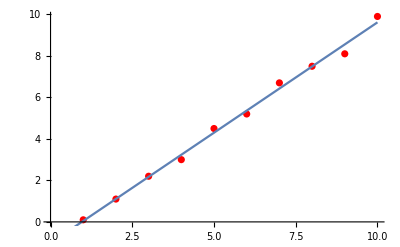

```mathematica
(* LinReg Function *)
LinReg[x_,y_]:=
Module[{A,Q,R},
A=ConstantArray[1,{Length[x],2}];
A[[All,1]]=x;
{Q,R}=QRDecomposition[A];
LinearSolve[R,Q.y]];
(* Data *)
x = {1, 2, 3, 4, 5, 6, 7, 8, 9, 10};
y = {0.1, 1.1, 2.2, 3.0, 4.5, 5.2, 6.7, 7.5, 8.1, 9.9};
(* Function Call *)
sol=LinReg[x,y];
(* Plot *)
Print[Show[ListPlot[y,PlotStyle->Red],Plot[sol[[1]]*t+sol[[2]],{t,0,10}]]]
```